```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## Z' Z' X → Z' X

```mathematica
(* Y(k1) Y(k2) X(k3)->Y(p1) X(p2) *)
(*4D,Mandelstam variables,NR applied per-term*)

FCClearScalarProducts[];

(*Scalar products: 4D Mandelstam*)
SP[k1,k1]=mY^2;SP[k2,k2]=mY^2;
SP[k3,k3]=mX^2;SP[p1,p1]=mY^2;SP[p2,p2]=mX^2;

SP[k1,k2]=(s12-2 mY^2)/2;
SP[k1,k3]=(s13-mY^2-mX^2)/2;
SP[k1,p1]=mY^2-t1/2;
SP[k2,p1]=mY^2-t2/2;
SP[k3,p1]=(mX^2+mY^2-t3)/2;
SP[k2,k3]=-(s12-2 mY^2)/2-(s13-mY^2-mX^2)/2+(mY^2-t1/2)+(mY^2-t2/2)+(mX^2+mY^2-t3)/2-(3 mY^2)/2;

(*p2=k1+k2+k3-p1 cross terms*)
SP[p2,k1]=SP[k1,k1]+SP[k1,k2]+SP[k1,k3]-SP[k1,p1];
SP[p2,k2]=SP[k1,k2]+SP[k2,k2]+SP[k2,k3]-SP[k2,p1];
SP[p2,k3]=SP[k1,k3]+SP[k2,k3]+SP[k3,k3]-SP[k3,p1];
SP[p2,p1]=SP[k1,p1]+SP[k2,p1]+SP[k3,p1]-SP[p1,p1];

(*NR definitions*)
sqrtsNR=2 mY+mX;
sNR=sqrtsNR^2;
EYf=(sNR+mY^2-mX^2)/(2 sqrtsNR);
NRrules={s12->4 mY^2,s13->(mY+mX)^2,t1->2 mY^2-2 mY EYf,t2->2 mY^2-2 mY EYf,t3->mX^2+mY^2-2 mX EYf};

(*Amplitudes (4D) with propagators inline*)
qFlow={k1,k2,-p1};
idx={μ,ν,ρ};
ampD[{a_,b_,c_}]:=Module[{qa,qb,ia,ib,ic,P1,P2,d1,d2},qa=qFlow⟦a⟧;ia=idx⟦a⟧;
qb=qFlow⟦b⟧;ib=idx⟦b⟧;
ic=idx⟦c⟧;
P1=k3+qa;P2=k3+qa+qb;
d1=ExpandScalarProduct[SP[P1,P1]]-mX^2;
d2=ExpandScalarProduct[SP[P2,P2]]-mX^2;
SpinorUBar[p2,mX].GA[ic].(GS[P2]+mX).GA[ib].(GS[P1]+mX).GA[ia].SpinorU[k3,mX]/(d1 d2)//DiracSimplify];
perms=Permutations[{1,2,3}];
amps=Table[ampD[perms⟦i⟧],{i,1,6}];

(*Process one term: polarization sums as multiplicative tensors*)
proc[i_,j_]:=Module[{cc,Mij},cc=ComplexConjugate[amps⟦j⟧]/. {μ->μp,ν->νp,ρ->ρp};
Mij=FermionSpinSum[amps⟦i⟧ cc]*
(-MT[μ,μp]+FV[k1,μ] FV[k1,μp]/mY^2)*
(-MT[ν,νp]+FV[k2,ν] FV[k2,νp]/mY^2)*
(-MT[ρ,ρp]+FV[p1,ρ] FV[p1,ρp]/mY^2)//Contract//DiracSimplify;
Mij=Mij/. NRrules;
Mij=PowerExpand[Mij]/.mY->mX/r//FullSimplify[#,r>1&&mX>0]&];
```

```mathematica
(* Write each term to file *)
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YYX_YX_vP_v2"}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];
```

```mathematica
(*Diagonal terms*)
Do[Print["(",i,",",i,") ..."];
term=proc[i,i];
Put[term,FileNameJoin[{outputDir,"diag_"<>ToString[i]<>"_"<>ToString[i]<>".m"}]];
Clear[term];
Print["  Done."];,{i,1,6}];

(*Off-diagonal terms (already multiplied by 2)*)
Do[Print["(",i,",",j,") ..."];
term=2 proc[i,j];
Put[term,FileNameJoin[{outputDir,"offdiag_"<>ToString[i]<>"_"<>ToString[j]<>".m"}]];
Clear[term];
Print["  Done."];,{i,1,6},{j,i+1,6}];

Print["\nAll 21 terms saved to: ",outputDir];
```

(1,1) ...

Done.

(2,2) ...

Done.

(3,3) ...

Done.

(4,4) ...

Done.

(5,5) ...

Done.

(6,6) ...

Done.

(1,2) ...

Done.

(1,3) ...

Done.

(1,4) ...

Done.

(1,5) ...

Done.

(1,6) ...

Done.

(2,3) ...

Done.

(2,4) ...

Done.

(2,5) ...

Done.

(2,6) ...

Done.

(3,4) ...

Done.

(3,5) ...

Done.

(3,6) ...

Done.

(4,5) ...

Done.

(4,6) ...

Done.

(5,6) ...

Done.

All 21 terms saved to: /home/gab/Desktop/PyCharm_env/secluded_DM/mathematica/MsqTerms_YYX_YX_vP_v2

## Load and sum all terms

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YYX_YX_vP_v2"}];
files=FileNames["*.m",outputDir];
Print["Loading ",Length[files]," terms..."];
MsqTotal=0;
Do[term=Get[f];MsqTotal+=term;Clear[term];,{f,files}];
MsqAvgNR=MsqTotal/18//Simplify;
```

Loading 21 terms...

```mathematica
MsqAvgNR//FullSimplify
```

```mathematica
sqrtsNR=2 mY+mX;
sNR=sqrtsNR^2;
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2 a b-2 a c-2 b c;
lambdaNR=Kallen[sNR,mY^2,mX^2]/.mY->mX/r//Simplify;

(*Phase space factor from Eq.(A11) of 1609.02555;factor of 2=integral of d(cos θ) over [-1,1];S=1*)
sigmav2NR=MsqAvgNR*Sqrt[lambdaNR]/(64 Pi mY^2 mX sNR);

(*Restore coupling: gD^6=(4 π alphaX)^3;*)
sigmav2NR=PowerExpand[(4 Pi alphaX)^3*sigmav2NR]/.mY->mX/r//Simplify
```

(4 alphaX^3 π^2 r^5 √(3+8 r+4 r^2) (195+1156 r+4670 r^2+9444 r^3+12214 r^4+11192 r^5+6732 r^6+2272 r^7+320 r^8))/(√3 mX^5 (2+r)^3 (1+2 r)^4 (-1+r+4 r^2+2 r^3)^2)

```mathematica
(*Delta3: sigmav2=Delta3*alphaX^3/mX^5;*)
Delta3=PowerExpand[sigmav2NR*mX^5/alphaX^3]//FullSimplify
```

(4 π^2 r^5 √(1+4/3 r (2+r)) (195+2 r (578+r (2335+r (4722+r (6107+2 r (2798+r (1683+8 r (71+10 r)))))))))/((2+r)^3 (1+2 r)^4 (-1+r+2 r^2 (2+r))^2)

```mathematica
N[Delta3/. r->1]
N[Delta3/. r->2]
N[Delta3/.r->10]
N[Delta3/.r->100]
```

54.0375

144.021

1610.53

21931.3

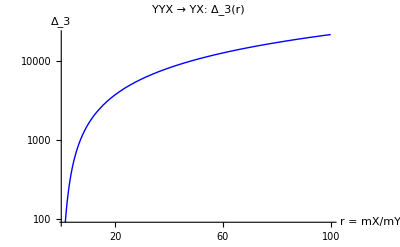

```mathematica
Plot[Delta3, {r, 1.5, 100},
 PlotRange -> All,
 ScalingFunctions -> {"Linear", "Log"},
 AxesLabel -> {"r = mX/mY", "Δ_3"},
 PlotLabel -> "YYX → YX:  Δ_3(r)",
 PlotStyle -> {Thick, Blue}]
```

```mathematica
Print["\n===== Delta_3(r) for selected mass ratios ====="];
Print[PaddedForm[
  TableForm[
   Table[{r0, N[Delta3 /. r -> r0, 8]}, {r0, {1.5,2, 3, 5, 7, 10, 15, 20, 50, 100}}],
   TableHeadings -> {None, {"r = mX/mY", "Delta_3"}}], {8, 4}]];
```

===== Delta_3(r) for selected mass ratios =====

r = mX/mY | Delta_3
    1.5000 |    92.1071
        2 |   144.0214
        3 |   276.6490
        5 |   611.2223
        7 |   994.0010
       10 |  1610.5281
       15 |  2688.2713
       20 |  3793.1464
       50 |  10560.7570
      100 |  21931.2770

```mathematica
PowerExpand[(4 π^2 r^5 √(1+4/3 r (2+r)) (195+2 r (578+r (2335+r (4722+r (6107+2 r (2798+r (1683+8 r (71+10 r)))))))))/((2+r)^3 (1+2 r)^4 (-1+r+2 r^2 (2+r))^2)/.r-> 1/rv]//FullSimplify
```

(4 π^2 √(((2+rv) (2+3 rv))/rv^2) (320+rv (2272+rv (6732+rv (11192+rv (12214+rv (9444+rv (4670+rv (1156+195 rv)))))))))/(√3 (2+rv)^4 (1+2 rv)^3 (2+rv (4+rv-rv^2))^2)

```mathematica
PowerExpand[ (320+rv (2272+rv (6732+rv (11192+rv (12214+rv (9444+rv (4670+rv (1156+195 rv))))))))]
```

320+rv (2272+rv (6732+rv (11192+rv (12214+rv (9444+rv (4670+rv (1156+195 rv)))))))